```mathematica
eqs =Table[x^(2i) + y^(2i) ==2,{i,1,5}];
```

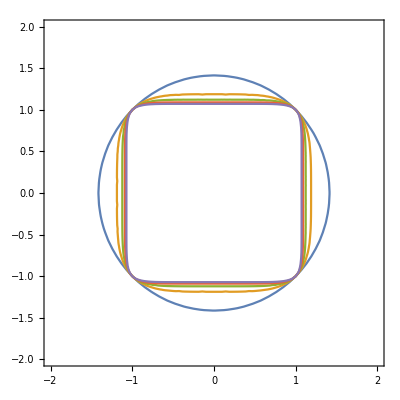

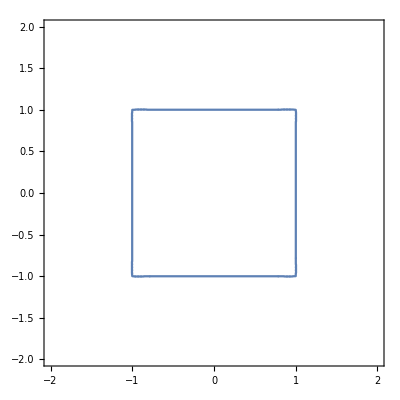

```mathematica
ContourPlot[eqs,{x,-2,2},{y,-2,2}]
ContourPlot[x^100+y^100==2,{x,-2,2},{y,-2,2}]
```

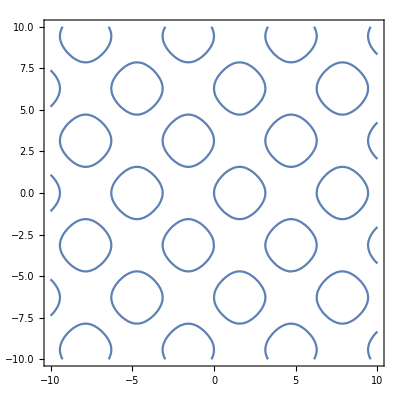

```mathematica
a = 10;
ContourPlot[{(Sin[x^1]+Cos[y^1])^2==1},{x,-a,a},{y,-a,a}]
```

```mathematica
a = 10;
ListAnimate[Table[ContourPlot[{(Sin[x^2]+Cos[y^2])^2==k},{x,-a,a},{y,-a,a},ContourStyle->Directive[RGBColor[1.,0.06,0.97],Opacity[0.4]]],{k,0,1,.05}]]
```

```mathematica
a = 2; k =0.5;
plot1=ContourPlot3D[(Sin[x^2]+Cos[y^2]+Sin[z^2])==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False]
Export["torso.obj",plot1]
```

-Graphics3D-

```mathematica
a = 1.4; k =0.5; i =4;
plot1=ContourPlot3D[(Sin[x^i]+Cos[y^i]+Sin[z^i])==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False]
```

-Graphics3D-

```mathematica
a = 1.4; k =0.5; i =10;
plot1=ContourPlot3D[(Sin[x^i]+Cos[y^i]+Sin[z^i])==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
a = 3; k =0.5; 
SeedRandom[6];
r1= RandomReal[]
r2 = RandomReal[]
r3 = RandomReal[]
ContourPlot3D[(Sin[x^2 r1]+Cos[y^2 r2] +Sin[z^2 r3])==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False]
```

0.254505

0.961561

0.515297

-Graphics3D-

```mathematica
Clear["Global`*"]
SeedRandom[2];
a = 10; k = 1;
freq = Table[2RandomReal[],15];
f[x_,y_,z_] = Sum[Sin[x freq[[i]]] + Sin[y freq[[i+1]]] + Sin[z freq[[i+2]]],{i,1,Length[freq]-2}]-z^1.4;
model=ContourPlot3D[f[x,y,z]==1,{x,-a,a},{y,-a,a},{z,0,10},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["terrain8.obj",model]
```

terrain8.obj

```mathematica
Clear["Global`*"]
SeedRandom[2];
a = 10; k = 0; α = 10; i =4;
f[x_,y_,z_] = x^i + y^i +z^i - (x^(i/2) + y^(i/2)+z^(i/2))^2 + α (x^(i/2) + y^(i/2) + z^(i/2));
model=ContourPlot3D[f[x,y,z]==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["pipes.obj",model]
```

pipes.obj

```mathematica
Clear["Global`*"]
SeedRandom[2];
a = 10; k = 0; α = 10; i =12;
f[x_,y_,z_] = x^i + y^i +z^i - (x^(i/2) + y^(i/2)+z^(i/2))^2 + α (x^(i/2) + y^(i/2) + z^(i/2));
model=ContourPlot3D[f[x,y,z]==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False,Boxed->False,Axes->False,PlotPoints->100]
```

-Graphics3D-

```mathematica
Export["square_pipes.obj",model]
```

square_pipes.obj

```mathematica
Clear["Global`*"]
SeedRandom[2];
a = 10; k = 0; α = 10; i =Sqrt[5]//N;
f[x_,y_,z_] = x^i + y^i +z^i - (x^(i/2) + y^(i/2)+z^(i/2))^2 + α (x^(i/2) +y^(i/2) +z^(i/2));
model=ContourPlot3D[f[Abs[x],Abs[y],Abs[z]]==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[0.4]],Contours->1,Mesh->False,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Export["pentagon_pipes.obj",model]
```

pentagon_pipes.obj

```mathematica
Clear["Global`*"]
SeedRandom[2];
a = 2; k = 1; α = 10; i =20//N;
f[x_,y_,z_] =Exp[-.15(x^i + y^i + z^i )](x^i + y^i + z^i) +Exp[-.15((1/2 (x-y+√2 z))^i +(1/4 ((2+√2) x-(-2+√2) y-2 z))^i+(1/4 (-(-2+√2) x+(2+√2) y+2 z))^i)]((1/2 (x-y+√2 z))^i +(1/4 ((2+√2) x-(-2+√2) y-2 z))^i+(1/4 (-(-2+√2) x+(2+√2) y+2 z))^i);
model=ContourPlot3D[f[Abs[x],Abs[y],Abs[z]]==k,{x,-a,a},{y,-a,a},{z,-a,a},ContourStyle->Directive[RGBColor[1,0.06,0.97],Opacity[1]],Contours->1,Mesh->False,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
r1=RotationMatrix[θ,{1,0,0}]/.θ->Pi/4;
r2=RotationMatrix[θ,{0,1,0}]/.θ->Pi/4;
r3=RotationMatrix[θ,{0,0,1}]/.θ->Pi/4;
```

```mathematica
r1.(r2.(r3.{x,y,z}))//Simplify
```

{1/2 (x-y+√2 z),1/4 ((2+√2) x-(-2+√2) y-2 z),1/4 (-(-2+√2) x+(2+√2) y+2 z)}

```mathematica
r2=RotationMatrix[θ,{0,1,0}]/.θ->Pi/2
```

{{0,0,1},{0,1,0},{-1,0,0}}